```mathematica
Remove["Global`*"];
(*SetDirectory[""];*)
```

# Example: Cachipun Dynamics with different starting proportions

Here x,y,z represents rock, scissor, and paper, respectively

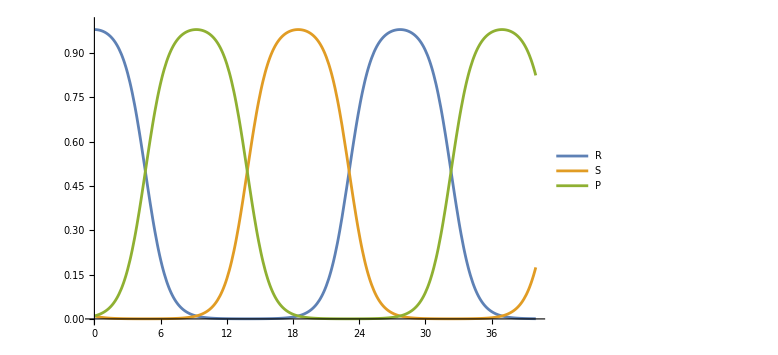

```mathematica
tmax=40;
r = 0.98;
p = 0.01;
s=0.01;
soln=First@NDSolve[{x'[t]==x[t]*(y[t]-z[t]),y'[t]==y[t](z[t]-x[t]), z'[t]==z[t](x[t]-y[t]),x[0]==r,y[0]==s,z[0]==p},{x,y,z},{t,0,tmax}];
P1=Plot[{x[t]/. soln,y[t]/. soln,z[t]/.soln},{t,0,tmax},PlotRange->{0,1},PlotLegends->{"R","S","P"},ImageSize->Large]
(*Export["grafico_ODE_RPS1.pdf",P1];*)
```

40

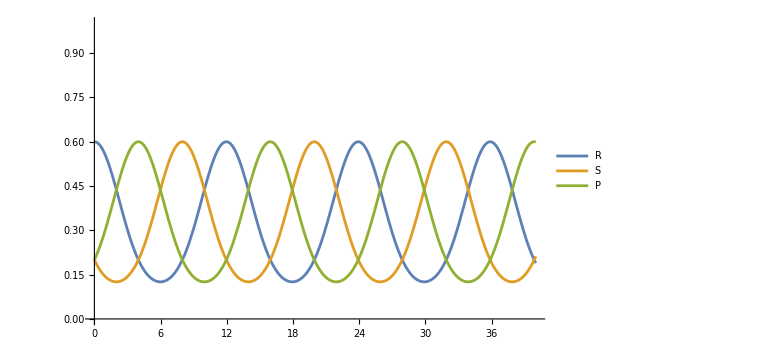

```mathematica
tmax=40
r = 0.6;
p = 0.2;
s=0.2;
soln=First@NDSolve[{x'[t]==x[t]*(y[t]-z[t]),y'[t]==y[t](z[t]-x[t]), z'[t]==z[t](x[t]-y[t]),x[0]==r,y[0]==s,z[0]==p},{x,y,z},{t,0,tmax}];
P2=Plot[{x[t]/. soln,y[t]/. soln,z[t]/.soln},{t,0,tmax},PlotRange->{0,1},PlotLegends->{"R","S","P"},ImageSize->Large]
(*Export["grafico_ODE_RPS2.pdf",P2];*)
```

400

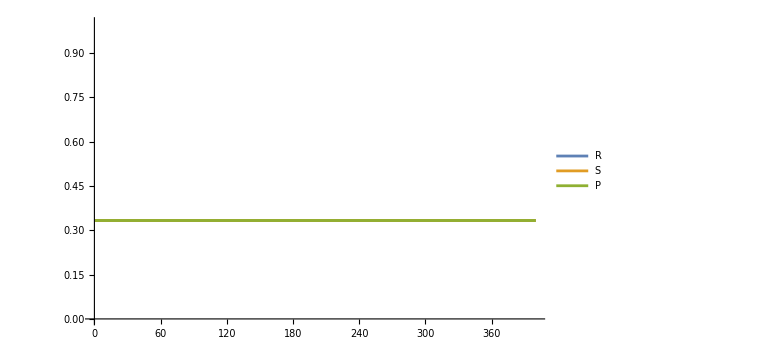

```mathematica
tmax=400
r = 1/3;
p =1/3;
s=1/3;
soln=First@NDSolve[{x'[t]==x[t]*(y[t]-z[t]),y'[t]==y[t](z[t]-x[t]), z'[t]==z[t](x[t]-y[t]),x[0]==r,y[0]==s,z[0]==p},{x,y,z},{t,0,tmax}];
P3=Plot[{x[t]/. soln,y[t]/. soln,z[t]/.soln},{t,0,tmax},PlotRange->{0,1},PlotLegends->{"R","S","P"},ImageSize->Large]
(*Export["grafico_ODE_RPS3.pdf",P3];*)
```